```mathematica
Quit
```

## Init

Load the package and set the base directory where intermediate files will be created:

```mathematica
AppendTo[$Path,ParentDirectory@NotebookDirectory[]];
Needs["AstronomicalDiaries`"]
```

```mathematica
$ADBase=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Data"}];
```

## Getting texts

Download the texts and metadata from Oracc and then create a file called revisdOracc.txt that can be edited to fix errors in the Oracc texts:

```mathematica
ADRevisedOraccExport[]
```

/Users/christopher/git/ComputableAstronomicalDiaries/InputTexts/revisedOracc.txt

## Parsing

Make sure that the OpenAI API key is set through SystemCredential:

```mathematica
(*SystemCredential["OPENAI_API_KEY"]="<your api key>"*)
```

Automatically find the mapping from line numbers to months:

```mathematica
ADLineMonths[];
```

If the automatically-generated mapping from line numbers to months was wrong, it can be hardcoded. The line below creates an editable file that can be used to hardcode the line-month mapping:

```mathematica
(*ADLineMonthHardcode["X102611"]*)
```

Find all the substrings that contain observations:

```mathematica
ADObservationIDs[];
```

Parse the observation substrings:

```mathematica
ADObservationParses[];
```

Put all the results together into an observations list:

```mathematica
AstronomicalDiaries`LineMonths`Private`lineMonths["RawLineMonths"]=;
```

```mathematica
observations=ADObservations[];
```

## Inferencing

### Model

```mathematica
GraphicsRow@{-Graphics-,-Graphics-}
```

-Graphics-

#### Key

### True model

```mathematica
Needs["AstronomicalDiaries`Astronomy`"]
```

```mathematica
timeRange={-12,12};
objectDistanceApproxParamsCache=<||>;

objectDistanceApproxParams[obj_,ref_,rel_,d_]:=
Lookup[
objectDistanceApproxParamsCache,
Key[{obj,ref,rel,d}],
objectDistanceApproxParamsCache[{obj,ref,rel,d}]=
Table[
objectDisplacement[obj,ref,DateObject[d,"Instant",TimeZone->$timeZone]+Quantity[ti,"Hours"]][[relationAxes[rel]]],
{ti,timeRange}
]
]
objectDistanceApproxParams[obj_List,ref_List,rel_List,d_List]:=MapThread[objectDistanceApproxParams,{obj,ref,rel,d}]
```

```mathematica
objectDistanceApprox[params_,t_]/;ArrayDepth[params]===1:=
(params[[2]]-params[[1]])/(timeRange[[2]]-timeRange[[1]])*(t-timeRange[[1]])+params[[1]]
objectDistanceApprox[params_,t_]/;ArrayDepth[params]===2:=
(params[[All,2]]-params[[All,1]])/(timeRange[[2]]-timeRange[[1]])*(t-timeRange[[1]])+params[[All,1]]
objectDistanceApprox[obj_,ref_,rel_,d_,t_]:=
objectDistanceApprox[objectDistanceApproxParams[obj,ref,rel,d],t]
```

### Updates

#### Utilities

```mathematica
normalArraySample[NormalDistribution[μ_List,σ_List]]:=RandomVariate[NormalDistribution[],Length[μ]]*σ+μ
normalArraySample[n_NormalDistribution]:=RandomVariate@n
```

#### Normal mean

μ\[Distributed]Normal(μ_0,σ_0)
y\[Distributed]Normal(μ,σ)

Samples μ with observed y

```mathematica
normalNormalMeanSample[NormalDistribution[μ0_,σ0_],σ_,ys_]:=
With[{σn2=(1/σ0^2+Length[ys]/σ^2)^-1},
RandomVariate@NormalDistribution[σn2(μ0/σ0^2+Total[ys]/σ^2),Sqrt[σn2]]
]
```

#### Normal variance

σ^2\[Distributed]InverseGamma(α,β)
y\[Distributed]Normal(μ,σ)

Samples σ^2 with observed y

```mathematica
normalNormalVarianceSample[InverseGammaDistribution[α_,β_],μ_,ys_]:=
RandomVariate@InverseGammaDistribution[α+(1/2)Length[ys],β+(1/2)Total[(ys-μ)^2]]
```

#### Normal regression

x\[Distributed]Normal(μ_0,σ_0)
y\[Distributed]Normal(m*x+b,σ)

Samples x with observed m, b and y

For many observations for the same x:

```mathematica
normalNormalRegressionSample[NormalDistribution[μ0_,σ0_],σ_,m_,b_,y_]:=
With[{σn2=(1/σ0^2+Total[m^2]/σ^2)^-1},
normalArraySample@NormalDistribution[σn2(μ0/σ0^2+(m.(y-b))/σ^2),Sqrt[σn2]]
]
```

For a vector of x_i:

```mathematica
normalNormalRegressionSample[NormalDistribution[μ0_List,σ0_List],σ_,m_,b_,y_]:=
With[{σn2=(1/σ0^2+m^2/σ^2)^-1},
normalArraySample@NormalDistribution[σn2(μ0/σ0^2+(m*(y-b))/σ^2),Sqrt[σn2]]
]
```

#### Time updates

Collecting terms in the formula for the approximate true position, we get that it is linear with t:

```mathematica
Collect[Block[{timeRange={tr1,tr2}},objectDistanceApprox[{p1,p2},t]*l],t]
```

(l (-p1+p2) t)/(-tr1+tr2)+l (p1-((-p1+p2) tr1)/(-tr1+tr2))

Therefore, this can be done with normalNormalRegressionSample with the following values:

m=(l (p2-p1))/(tr2-tr1)
b=l (p1-(tr1 (p2-p1))/(tr2-tr1))

#### Beta Bernoulli

p\[Distributed]Beta(α,β)
x\[Distributed]Bernoulli(p)

Samples p with observed x

```mathematica
betaBernoulliSample[BetaDistribution[α_,β_],xs_]:=
With[{t=Total[xs]},
RandomVariate@BetaDistribution[α+t,β+Length[xs]-t]
]
```

#### Binary normal mixture

m\[Distributed]Bernoulli(p)
x\[Distributed]Piecewise[{{Normal(μ_1,σ_1), m=0}, {Normal(μ_2,σ_2), m=1}}]

Samples m with observed x

```mathematica
logNormalPDF[NormalDistribution[μ_,σ_],x_]:=-(x-μ)^2/(2 σ^2)+1/2 (-Log[2]-Log[π])-Log[σ]
```

```mathematica
logSumExp[m_,level_:0]:=With[{c=Map[Max,m,{level}]},c+Log[Total[Exp[m-c],{level+1}]]]
```

```mathematica
binaryNormalMixtureSample[BernoulliDistribution[p_],n1_NormalDistribution,n2_NormalDistribution,xs_]:=
With[{
mLogProbs=With[{
p1=Log[p]+logNormalPDF[n1,xs],
p2=Log[1-p]+logNormalPDF[n2,xs]},
(*Exp[p1]/(Exp[p1]+Exp[p2])*)
p1-logSumExp[Transpose@{p1,p2},1]
]
},
Boole@MapThread[Greater,{mLogProbs,Log@RandomReal[{0,1},Length[mLogProbs]]}]
]
```

### Gibbs sampler

```mathematica
modelObservations=Select[observations,!#Damaged&&!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&&!MissingQ[#Time]&&!MissingQ[#Relation]&&!(MissingQ[#Cubits]&&MissingQ[#Fingers])&];
```

```mathematica
fitModel[observations_,steps_,vars_:{}]:=
Module[{res,c,timeCats,pPrior,p,m,μTimesPrior,μTimes,σ2TimesPrior,σ2Times,t,σ2Prior,σ2,lPrior,l,μOutlierPrior,μOutlier,σ2OutlierPrior,σ2Outlier,δParams,δStar,outliers,inliers},
(*Observed data*)
c=N[observationCubitsSigned/@observations];
timeCats=observations[[All,"Time"]];

(*Priors and initialization*)
pPrior=BetaDistribution[1,1/2];p=RandomVariate@pPrior;
m=RandomVariate[BernoulliDistribution[p],Length@observations];
outliers=Position[m,0,{1},Heads->False][[All,1]];
inliers=Position[m,1,{1},Heads->False][[All,1]];

μTimesPrior=AssociationMap[NormalDistribution[0,6]&,Union@timeCats];
μTimes=RandomVariate/@μTimesPrior;
σ2TimesPrior=AssociationMap[InverseGammaDistribution[1/2,1/2]&,Union@timeCats];σ2Times=RandomVariate/@σ2TimesPrior;
t=normalArraySample@NormalDistribution[Lookup[μTimes,timeCats],Sqrt@Lookup[σ2Times,timeCats]];

σ2Prior=InverseGammaDistribution[1/2,1/2];σ2=RandomVariate@σ2Prior;
(*lPrior=NormalDistribution[1/2,1/2];l=RandomVariate@lPrior;*)
lPrior=NormalDistribution[2,1/2];l=RandomVariate@lPrior;

μOutlierPrior=NormalDistribution[];μOutlier=RandomVariate@μOutlierPrior;
(*TODO: Make higher variance*)
σ2OutlierPrior=InverseGammaDistribution[1.5,2];σ2Outlier=RandomVariate@σ2OutlierPrior;

δParams=objectDistanceApproxParams[
observations[[All,"Object"]],
observations[[All,"Reference"]],
observations[[All,"Relation"]],
observations[[All,"Date"]]
];

(*Updates*)
res=Reap@GeneralUtilities`MonitoredScan[
Function[
(*Compute true distances*)
δStar=objectDistanceApprox[δParams,t];

l=normalNormalRegressionSample[lPrior,Sqrt[σ2],δStar[[inliers]],0,c[[inliers]]];
(*l=normalNormalRegressionSampleOLD[lPrior,Sqrt[σ2],Pick[δStar,m,1],Pick[c,m,1]];*)
σ2=normalNormalVarianceSample[σ2Prior,δStar[[inliers]]*l,c[[inliers]]];

μOutlier=normalNormalMeanSample[μOutlierPrior,Sqrt[σ2Outlier],c[[outliers]]];
σ2Outlier=normalNormalVarianceSample[σ2OutlierPrior,μOutlier,c[[outliers]]];

m=binaryNormalMixtureSample[
BernoulliDistribution[p],
NormalDistribution[δStar*l,Sqrt[σ2]],
NormalDistribution[μOutlier,Sqrt[σ2Outlier]],
c
];
outliers=Position[m,0,{1},Heads->False][[All,1]];
inliers=Position[m,1,{1},Heads->False][[All,1]];

p=betaBernoulliSample[pPrior,m];

t[[inliers]]=normalNormalRegressionSample[
NormalDistribution[Lookup[μTimes,timeCats[[inliers]]],Sqrt@Lookup[σ2Times,timeCats[[inliers]]]],
Sqrt[σ2],
(l(δParams[[inliers,2]]-δParams[[inliers,1]]))/(timeRange[[2]]-timeRange[[1]]),
l(δParams[[inliers,1]]-(timeRange[[1]](δParams[[inliers,2]]-δParams[[inliers,1]]))/(timeRange[[2]]-timeRange[[1]])),
c[[inliers]]
];
t[[outliers]]=normalArraySample@NormalDistribution[Lookup[μTimes,timeCats[[outliers]]],Sqrt@Lookup[σ2Times,timeCats[[outliers]]]];

Scan[
With[{obsT=Pick[t,timeCats,#]},
μTimes[#]=normalNormalMeanSample[μTimesPrior[#],Sqrt[σ2Times[#]],obsT];
σ2Times[#]=normalNormalVarianceSample[σ2TimesPrior[#],μTimes[#],obsT]
]&,
Keys@μTimes
];

Sow@KeyTake[vars]@<|
"p"->p,
"m"->m,
"μTimes"->μTimes,
"σ2Times"->σ2Times,
"t"->t,
"l"->l,
"σ2"->σ2,
"μOutlier"->μOutlier,
"σ2Outlier"->σ2Outlier
|>
],
Range[steps]
];

res[[2,1]]
]
```

```mathematica
chains=Table[fitModel[modelObservations,2000,{"p","m","μTimes","σ2Times","t","l","σ2","μOutlier","σ2Outlier"}],4];//EchoTiming;
samples=Catenate@chains[[All,500;;]];
```

29.5386

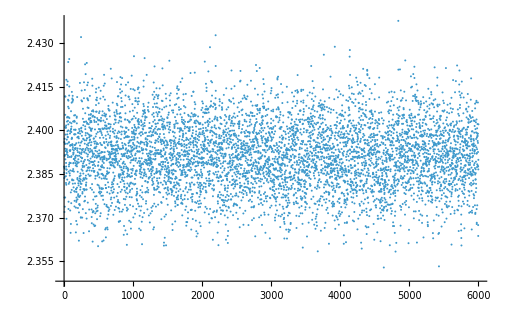

```mathematica
ListPlot[1/samples[[All,"l"]],PlotRange->All]
```

```mathematica
ArrayPlot@samples[[All,"m"]]
```

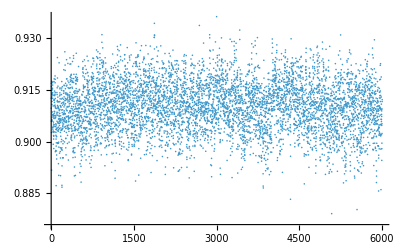

```mathematica
ListPlot[samples[[All,"p"]]]
```

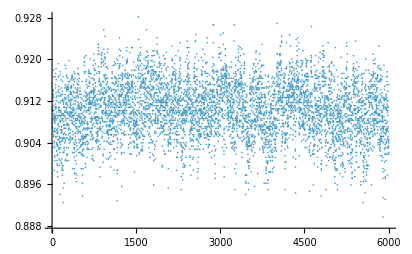

```mathematica
ListPlot[Mean@Transpose@samples[[All,"m"]]]
```

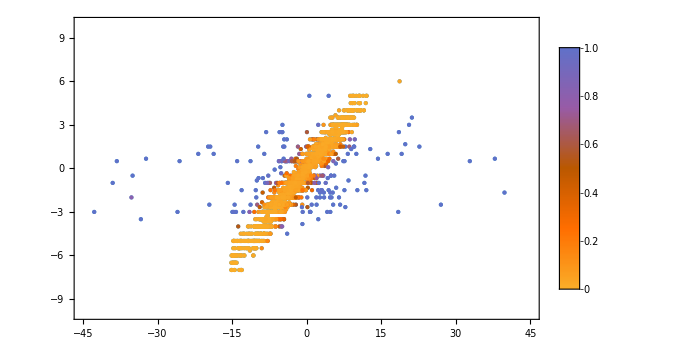

```mathematica
PointValuePlot[
Transpose[{
objectDistanceApprox[
modelObservations[[All,"Object"]],
modelObservations[[All,"Reference"]],
modelObservations[[All,"Relation"]],
modelObservations[[All,"Date"]],
samples[[-1,"t"]]
],
N@*observationCubitsSigned/@modelObservations
}]->1-Mean@samples[[All,"m"]],
AspectRatio->1/GoldenRatio,
PlotStyle->PointSize[Small],
PlotLegends->Automatic,
PlotRange->{{-45,45},{-10,10}}
]
```

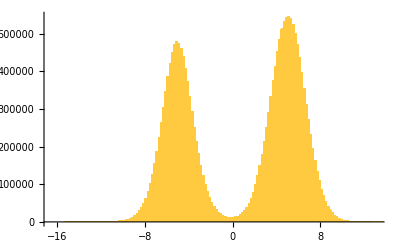

```mathematica
Histogram[Catenate@samples[[All,"t"]],{0.2}]
```

```mathematica
timing=ResourceFunction["EvaluationTiming"][fitModel[modelObservations,2000,{"p","m","μTimes","σ2Times","t","l","σ2","μOutlier","σ2Outlier"}]];
```

```mathematica
Dataset[timing]
```

## Old Gibbs samplers

### Original

```mathematica
Module[{normalNormalMeanSample,normalNormalVarianceSample,normalNormalRegressionSample,betaBernoulliSample,binaryNormalMixtureSample},

normalNormalMeanSample[NormalDistribution[μ0_,σ0_],σ_,ys_]:=
With[{σn2=(1/σ0^2+Length[ys]/σ^2)^-1},
RandomVariate@NormalDistribution[σn2(μ0/σ0^2+Total[ys]/σ^2),Sqrt[σn2]]
];

normalNormalVarianceSample[InverseGammaDistribution[α_,β_],μ_,ys_]:=
RandomVariate@InverseGammaDistribution[α+(1/2)Length[ys],β+(1/2)Total[(ys-μ)^2]];

normalNormalRegressionSample[NormalDistribution[μ0_,σ0_],σ_,xs_,ys_]:=
With[{σn2=(1/σ0^2+Total[xs^2]/σ^2)^-1},
RandomVariate@NormalDistribution[σn2(μ0/σ0^2+(xs.ys)/σ^2),Sqrt[σn2]]
];

betaBernoulliSample[BetaDistribution[α_,β_],xs_]:=
With[{t=Total[xs]},
RandomVariate@BetaDistribution[α+t,β+Length[xs]-t]
];

binaryNormalMixtureSample[n1_NormalDistribution,d1_,n2_NormalDistribution,d2_,p_]:=
With[{
mLogProbs=With[{
p1=Log[p]+logNormalPDF[n1,d1],
p2=Log[1-p]+logNormalPDF[n2,d2]},
(*Exp[p1]/(Exp[p1]+Exp[p2])*)
p1-logSumExp[Transpose@{p1,p2},1]
]
},
Boole@MapThread[Greater,{mLogProbs,Log@RandomReal[{0,1},Length[mLogProbs]]}]
];

fitModelOLD[observations_,steps_,vars_:{}]:=
Module[{n,c,timeCats,allTimeCats,pPrior,p,mPrior,m,μTimesPrior,μTimes,σ2TimesPrior,σ2Times,t,σ2Prior,σ2,lPrior,l,μOutlierPrior,μOutlier,σ2OutlierPrior,σ2Outlier,observationDistanceRanges,δStar,res},

(*Observed data*)
n=Length[observations];
c=N@*observationCubitsSigned/@observations;
timeCats=observations[[All,"Time"]];
allTimeCats=Union@timeCats;

(*Priors*)
pPrior=BetaDistribution[1,1/2];p=RandomVariate@pPrior;
mPrior=BernoulliDistribution[p];m=RandomVariate[mPrior,n];

μTimesPrior=AssociationMap[NormalDistribution[0.,6.]&,allTimeCats];μTimes=RandomVariate/@μTimesPrior;
σ2TimesPrior=AssociationMap[InverseGammaDistribution[0.5,0.5]&,allTimeCats];σ2Times=RandomVariate/@σ2TimesPrior;
t=RandomVariate[NormalDistribution[],n]*Sqrt[Lookup[σ2Times,timeCats]]+Lookup[μTimes,timeCats];

σ2Prior=InverseGammaDistribution[0.5,0.5];σ2=RandomVariate@σ2Prior;
lPrior=NormalDistribution[2.,0.5];l=RandomVariate@lPrior;

μOutlierPrior=NormalDistribution[];μOutlier=RandomVariate@μOutlierPrior;
(*TODO: Make higher variance*)
σ2OutlierPrior=InverseGammaDistribution[1.5,2];σ2Outlier=RandomVariate@σ2OutlierPrior;

observationDistanceRanges=Lookup[objectDistanceApproxParamsCache,{#Object,#Reference,#Relation,#Date}&/@observations];

(*Updates*)
res=Reap@GeneralUtilities`MonitoredScan[Function[
δStar=(observationDistanceRanges[[All,-1]]-observationDistanceRanges[[All,1]])/(timeRange[[2]]-timeRange[[1]])*(t-timeRange[[1]])+observationDistanceRanges[[All,1]];

l=normalNormalRegressionSample[lPrior,Sqrt[σ2],Pick[δStar,m,1],Pick[c,m,1]];
σ2=normalNormalVarianceSample[σ2Prior,Pick[δStar*l,m,1],Pick[c,m,1]];

μOutlier=normalNormalMeanSample[μOutlierPrior,Sqrt[σ2Outlier],Pick[c,m,0]];
σ2Outlier=normalNormalVarianceSample[σ2OutlierPrior,μOutlier,Pick[c,m,0]];

With[
{
indicesUnmasked=Position[m,1,{1},Heads->False][[All,1]],
rangesUnmasked=Pick[observationDistanceRanges,m,1],
timeCatsUnmasked=Pick[timeCats,m,1],
cUnmasked=Pick[c,m,1]
},
{
tμ0=Lookup[μTimes,timeCatsUnmasked],
tσ02=Lookup[σ2Times,timeCatsUnmasked],
x=(l*(rangesUnmasked[[All,2]]-rangesUnmasked[[All,1]]))/(timeRange[[2]]-timeRange[[1]]),
y=(l(rangesUnmasked[[All,1]]* timeRange[[2]]-rangesUnmasked[[All,2]]* timeRange[[1]]))/(timeRange[[2]]-timeRange[[1]])
},
{
tμ=(x(cUnmasked-y)*tσ02+tμ0*σ2)/(x^2*tσ02+σ2),
tσ2=√((tσ02 σ2)/(x^2 tσ02+σ2))
},
t[[indicesUnmasked]]=RandomVariate[NormalDistribution[0.,1.],Total[m]]*Sqrt[tσ2]+tμ;
(*TODO: Is this next part right?*)
t[[Complement[Range[n],indicesUnmasked]]]=RandomVariate[NormalDistribution[0.,1.],n-Total[m]]*Sqrt[Lookup[σ2Times,Pick[timeCats,m,0]]]+Lookup[μTimes,Pick[timeCats,m,0]]
];

Scan[With[{obs=Pick[t,timeCats,#]},
μTimes[#]=normalNormalMeanSample[μTimesPrior[#],Sqrt[σ2Times[#]],obs];
σ2Times[#]=normalNormalVarianceSample[σ2TimesPrior[#],μTimes[#],obs]
]&,
allTimeCats
];

m=binaryNormalMixtureSample[
NormalDistribution[0.,1.],(c-δStar*l)/Sqrt[σ2],(*this is an optimization for NormalDistribution[δStar*l,Sqrt[σ2]],c,*)
NormalDistribution[μOutlier,Sqrt[σ2Outlier]],c,
p
];

p=betaBernoulliSample[pPrior,m];

Sow@KeyTake[vars]@<|
"p"->p,
"m"->m,
"μTimes"->μTimes,
"σ2Times"->σ2Times,
"t"->t,
"l"->l,
"σ2"->σ2,
"μOutlier"->μOutlier,
"σ2Outlier"->σ2Outlier
|>],
Range@steps
];

res[[2,1]]
]
]
```

### Aligned with new

```mathematica
Module[{binaryNormalMixtureSampleOLD},

binaryNormalMixtureSampleOLD[n1_NormalDistribution,d1_,n2_NormalDistribution,d2_,p_]:=
With[{
mLogProbs=With[{
p1=Log[p]+logNormalPDF[n1,d1],
p2=Log[1-p]+logNormalPDF[n2,d2]},
(*Exp[p1]/(Exp[p1]+Exp[p2])*)
p1-logSumExp[Transpose@{p1,p2},1]
]
},
Boole@MapThread[Greater,{mLogProbs,Log@RandomReal[{0,1},Length[mLogProbs]]}]
];

fitModelOLD[observations_,steps_,vars_:{}]:=
Module[{n,c,timeCats,allTimeCats,pPrior,p,mPrior,m,μTimesPrior,μTimes,σ2TimesPrior,σ2Times,t,σ2Prior,σ2,lPrior,l,μOutlierPrior,μOutlier,σ2OutlierPrior,σ2Outlier,observationDistanceRanges,δStar,res,inliers,outliers},

(*Observed data*)
n=Length[observations];
c=N@*observationCubitsSigned/@observations;
timeCats=observations[[All,"Time"]];
allTimeCats=Union@timeCats;

(*Priors*)
pPrior=BetaDistribution[1,1/2];p=RandomVariate@pPrior;
mPrior=BernoulliDistribution[p];m=RandomVariate[mPrior,n];
outliers=Position[m,0,{1},Heads->False][[All,1]];
inliers=Position[m,1,{1},Heads->False][[All,1]];

μTimesPrior=AssociationMap[NormalDistribution[0.,6.]&,allTimeCats];μTimes=RandomVariate/@μTimesPrior;
σ2TimesPrior=AssociationMap[InverseGammaDistribution[0.5,0.5]&,allTimeCats];σ2Times=RandomVariate/@σ2TimesPrior;
t=RandomVariate[NormalDistribution[],n]*Sqrt[Lookup[σ2Times,timeCats]]+Lookup[μTimes,timeCats];

σ2Prior=InverseGammaDistribution[0.5,0.5];σ2=RandomVariate@σ2Prior;
lPrior=NormalDistribution[2.,0.5];l=RandomVariate@lPrior;

μOutlierPrior=NormalDistribution[];μOutlier=RandomVariate@μOutlierPrior;
(*TODO: Make higher variance*)
σ2OutlierPrior=InverseGammaDistribution[1.5,2];σ2Outlier=RandomVariate@σ2OutlierPrior;

observationDistanceRanges=objectDistanceApproxParams[
observations[[All,"Object"]],
observations[[All,"Reference"]],
observations[[All,"Relation"]],
observations[[All,"Date"]]
];

(*Updates*)
res=Reap@GeneralUtilities`MonitoredScan[Function[
δStar=objectDistanceApprox[observationDistanceRanges,t];

l=normalNormalRegressionSample[lPrior,Sqrt[σ2],Pick[δStar,m,1],0,Pick[c,m,1]];
σ2=normalNormalVarianceSample[σ2Prior,δStar[[inliers]]*l,c[[inliers]]];

μOutlier=normalNormalMeanSample[μOutlierPrior,Sqrt[σ2Outlier],c[[outliers]]];
σ2Outlier=normalNormalVarianceSample[σ2OutlierPrior,μOutlier,c[[outliers]]];

With[
{
indicesUnmasked=Position[m,1,{1},Heads->False][[All,1]],
rangesUnmasked=Pick[observationDistanceRanges,m,1],
timeCatsUnmasked=Pick[timeCats,m,1],
cUnmasked=Pick[c,m,1]
},
{
tμ0=Lookup[μTimes,timeCatsUnmasked],
tσ02=Lookup[σ2Times,timeCatsUnmasked],
x=(l*(rangesUnmasked[[All,2]]-rangesUnmasked[[All,1]]))/(timeRange[[2]]-timeRange[[1]]),
y=(l(rangesUnmasked[[All,1]]* timeRange[[2]]-rangesUnmasked[[All,2]]* timeRange[[1]]))/(timeRange[[2]]-timeRange[[1]])
},
{
tμ=(x(cUnmasked-y)*tσ02+tμ0*σ2)/(x^2*tσ02+σ2),
tσ2=√((tσ02 σ2)/(x^2 tσ02+σ2))
},
t[[indicesUnmasked]]=RandomVariate[NormalDistribution[0.,1.],Total[m]]*Sqrt[tσ2]+tμ;
(*TODO: Is this next part right?*)
t[[Complement[Range[n],indicesUnmasked]]]=RandomVariate[NormalDistribution[0.,1.],n-Total[m]]*Sqrt[Lookup[σ2Times,Pick[timeCats,m,0]]]+Lookup[μTimes,Pick[timeCats,m,0]]
];

(*t[[inliers]]=normalNormalRegressionSample[
NormalDistribution[Lookup[μTimes,timeCats[[inliers]]],Sqrt@Lookup[σ2Times,timeCats[[inliers]]]],
Sqrt[σ2],
(l(δParams[[inliers,2]]-δParams[[inliers,1]]))/(timeRange[[2]]-timeRange[[1]]),
l(δParams[[inliers,1]]-(timeRange[[1]](δParams[[inliers,2]]-δParams[[inliers,1]]))/(timeRange[[2]]-timeRange[[1]])),
c[[inliers]]
];
t[[outliers]]=normalArraySample@NormalDistribution[Lookup[μTimes,timeCats[[outliers]]],Sqrt@Lookup[σ2Times,timeCats[[outliers]]]];*)

Scan[With[{obs=Pick[t,timeCats,#]},
μTimes[#]=normalNormalMeanSample[μTimesPrior[#],Sqrt[σ2Times[#]],obs];
σ2Times[#]=normalNormalVarianceSample[σ2TimesPrior[#],μTimes[#],obs]
]&,
allTimeCats
];

m=binaryNormalMixtureSampleOLD[
NormalDistribution[0.,1.],(c-δStar*l)/Sqrt[σ2],(*this is an optimization for NormalDistribution[δStar*l,Sqrt[σ2]],c,*)
NormalDistribution[μOutlier,Sqrt[σ2Outlier]],c,
p
];
(*m=binaryNormalMixtureSample[
mPrior,
NormalDistribution[δStar*l,Sqrt[σ2]],
NormalDistribution[μOutlier,Sqrt[σ2Outlier]],
c
];*)
outliers=Position[m,0,{1},Heads->False][[All,1]];
inliers=Position[m,1,{1},Heads->False][[All,1]];

p=betaBernoulliSample[pPrior,m];

Sow@KeyTake[vars]@<|
"p"->p,
"m"->m,
"μTimes"->μTimes,
"σ2Times"->σ2Times,
"t"->t,
"l"->l,
"σ2"->σ2,
"μOutlier"->μOutlier,
"σ2Outlier"->σ2Outlier
|>],
Range@steps
];

res[[2,1]]
]
]
```